```mathematica
Quit[]
```

Group of Divisor Waves DW-2 through DW-6

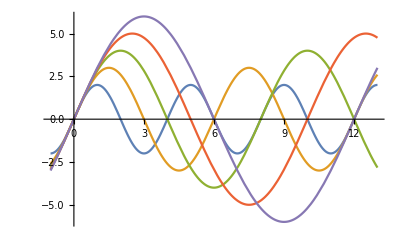

```mathematica
Plot[{2Sin[(x*Pi)/2],3Sin[(x*Pi)/3], 4Sin[(x*Pi)/4], 5Sin[(x*Pi)/5], 6Sin[(x*Pi)/6]}, {x,-1, 13}]
```

Equation for Infinite product of Divisor Waves

```mathematica
Plot[Product[Sin[(x*pi)/n], {n,2, Infinity}]]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[∏_(n=2)^∞ Sin[(x pi)/n]]

Product of Waves for 2 < n < 10

```mathematica
Product[Sin[(x/n)*Pi], {n,2, 10}]
```

Sin[(π x)/10] Sin[(π x)/9] Sin[(π x)/8] Sin[(π x)/7] Sin[(π x)/6] Sin[(π x)/5] Sin[(π x)/4] Sin[(π x)/3] Sin[(π x)/2]

Infinite Product of Divisor Waves

```mathematica
f[x1_, nm1_]:=Product[Sin[(x*Pi)/n],{n,2, nm1}];
```

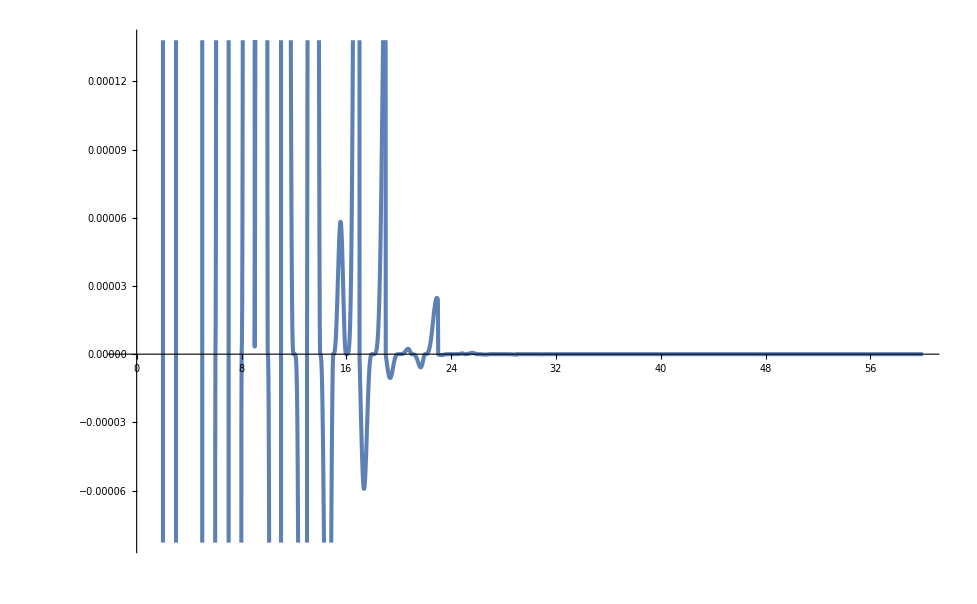

```mathematica
Plot[f[x1,x]//Evaluate,{x,-1,60}, PlotStyle-> Thickness[0.003], PlotStyle-> "SolarColors"]
```

Scaled Infinite Product of Divisor Waves

```mathematica
f[x1_, nm1_]:=Abs[Product[Sin[(x*Pi)/n],{n,2, nm1}]/(Product[Sin[(x*Pi)/n],{n,2, nm1}]Product[x, {n, 1, nm1}])];
```

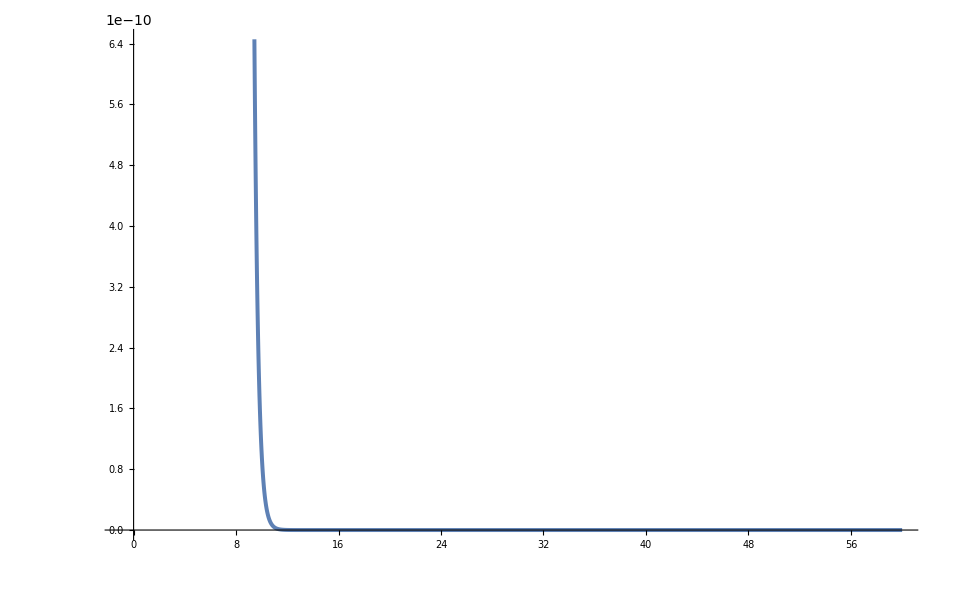

```mathematica
Plot[f[x1,x]//Evaluate,{x,-1,60}, PlotStyle-> Thickness[0.003], PlotStyle-> "SolarColors"]
```

Absolute Value Infinite Product of Divisor Waves

```mathematica
g[x2_,t2_,nm2_]:=Abs[Product[Sin[(x*Pi)/n],{n,2,nm2}]];
```

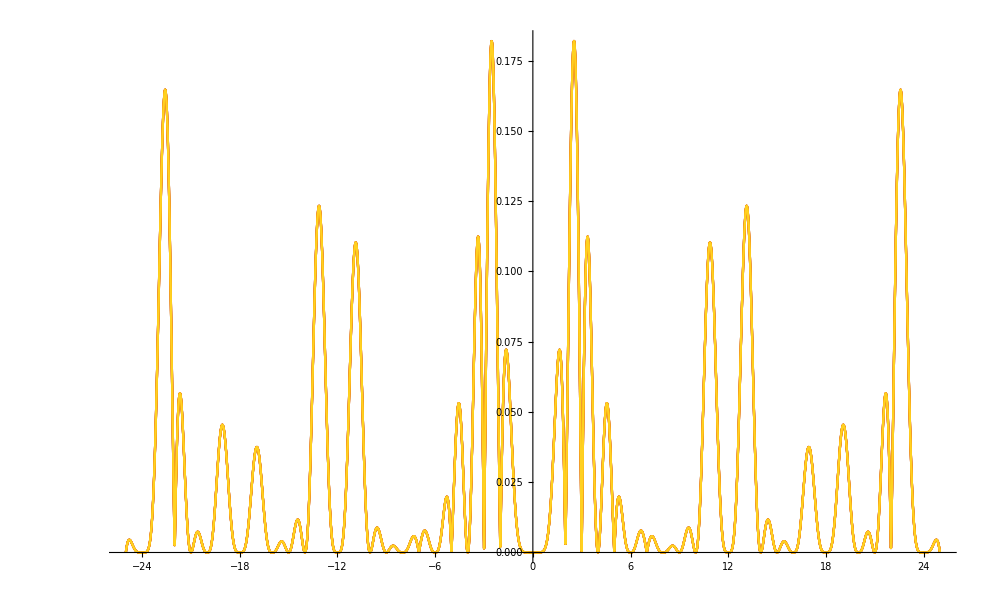

```mathematica
Plot[Table[g[x2,t2,9],{t2,{0,0.01,0.1,0.5,1,20}}]//Evaluate,{x,-25,25},PlotStyle-> "SolarColors"]
```

Factorial in denominator of Infinite Product of Divisor Waves

```mathematica
A[x3_,t3_,nm3_]:=Product[Sin[(x*Pi)/(n!)],{n,2,nm3}];
```

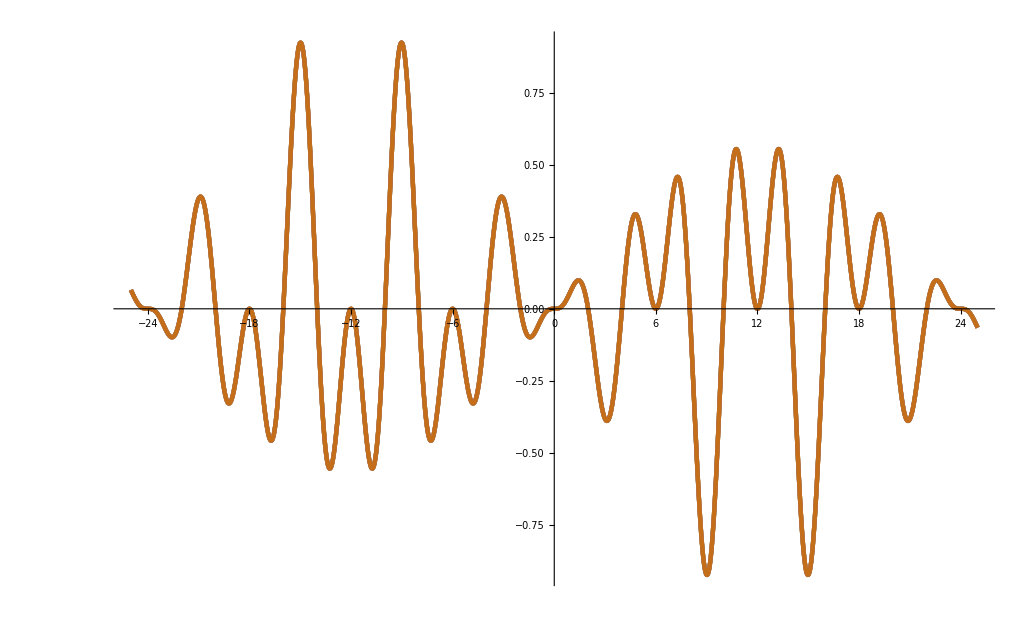

```mathematica
Plot[Table[A[x3,t3,4],{t3,{0,0.01,0.1,0.5,1,20}}]//Evaluate,{x,-25,25}, PlotStyle-> Thickness[0.003], PlotStyle-> "SolarColors"]
```

Absolute Value Factorial in denominator of Infinite Product of Divisor Waves

```mathematica
B[x4_,t4_,nm4_]:=Abs[Product[Sin[(x*Pi)/(n!)],{n,2,nm4}]];
```

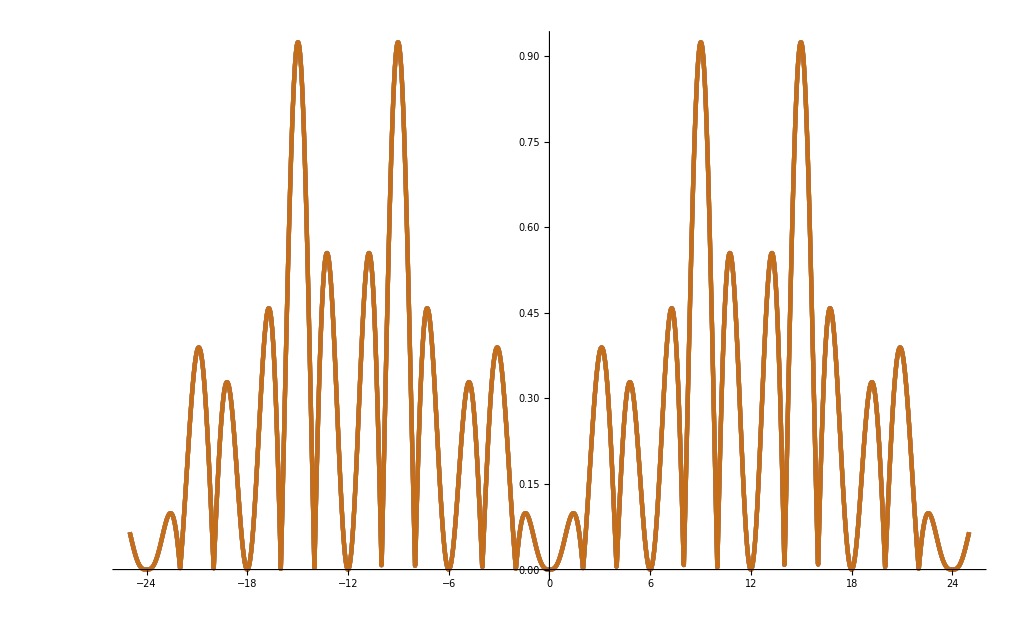

```mathematica
Plot[Table[B[x4,t4,4],{t4,{0,0.01,0.1,0.5,1,20}}]//Evaluate,{x,-25,25}, PlotStyle-> Thickness[0.003], PlotStyle-> "SolarColors"]
```

Square Divisor for Infinite Product of Divisor Waves

```mathematica
P[x5_,t5_,nm5_]:=Product[Sin[(x*Pi)/(n^2)],{n,2,nm5}];
```

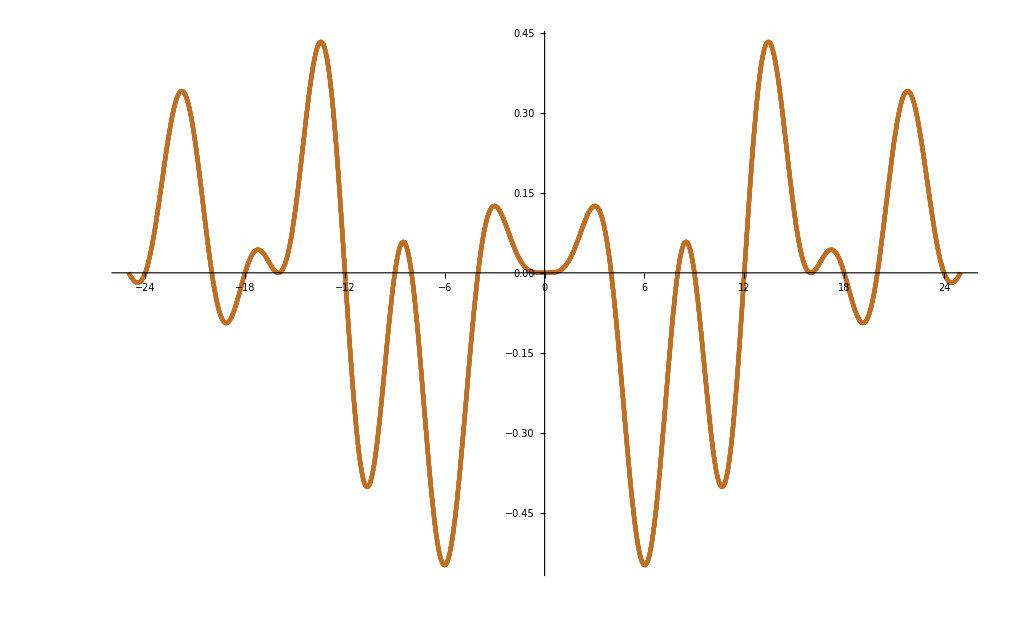

```mathematica
Plot[Table[P[x5,t5,5],{t5,{0,0.01,0.1,0.5,1,20}}]//Evaluate,{x,-25,25}, PlotStyle-> Thickness[0.003], PlotStyle-> "SolarColors"]
```

Absolute Value Square Divisor for Infinite Product of Divisor Waves

```mathematica
L[x6_,t6_,nm6_]:=Abs[Product[Sin[(x*Pi)/(n^2)],{n,2,nm6}]];
```

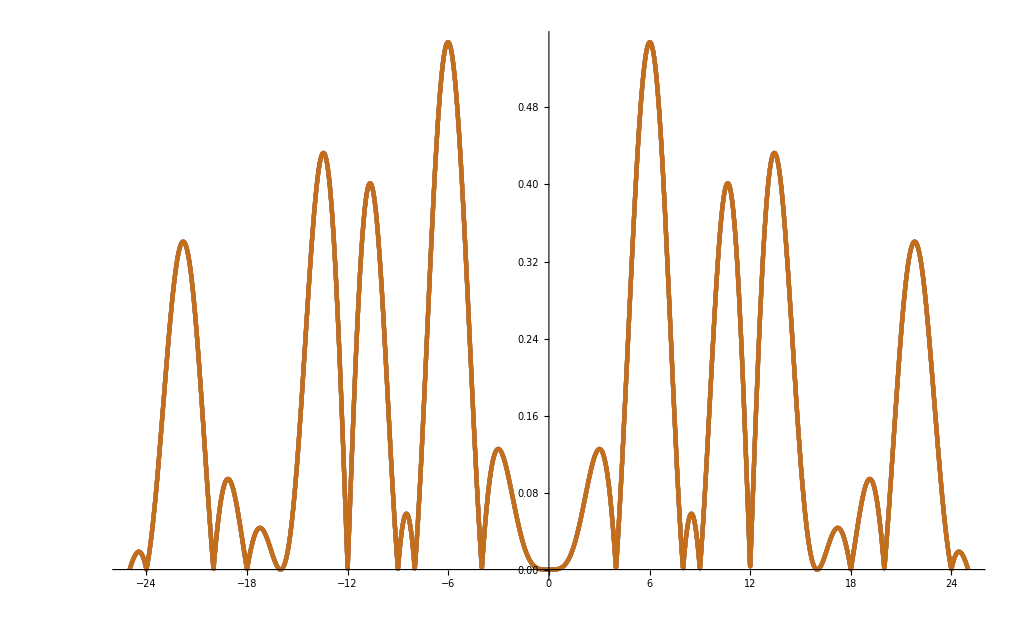

```mathematica
Plot[Table[L[x6,t6,5],{t6,{0,0.01,0.1,0.5,1,20}}]//Evaluate,{x,-25,25}, PlotStyle-> Thickness[0.003], PlotStyle-> "SolarColors"]
```

Sine x Secant for Infinite Product of Divisor Waves

```mathematica
M[x7_,t7_,nm7_]:=Product[Sin[(x*Pi)/(n^2)],{n,2,nm7}]*Product[Sec[(x*Pi)/(n^2)],{n,2,nm7}];
```

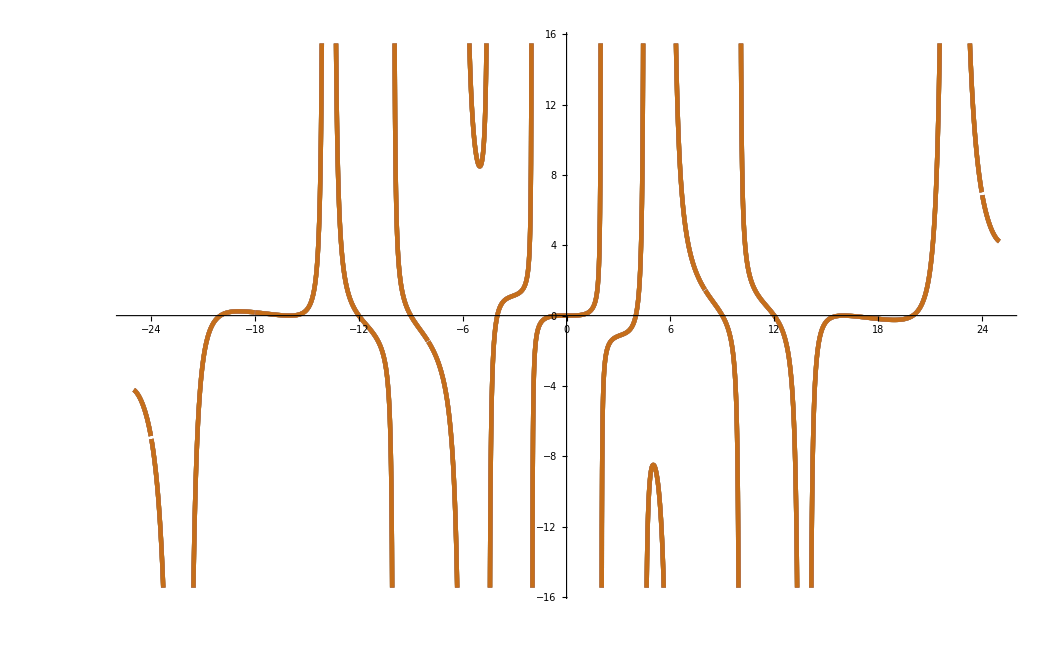

```mathematica
Plot[Table[M[x7,t7,4],{t7,{0,0.01,0.1,0.5,1,20}}]//Evaluate,{x,-25,25}, PlotStyle-> Thickness[0.003], PlotStyle-> "SolarColors"]
```

Absolute Value Sine x Secant for Infinite Product of Divisor Waves

```mathematica
h[x8_,t8_,nm8_]:=Abs[Product[Sin[(x*Pi)/(n^2)],{n,2,nm8}]*Product[Sec[(x*Pi)/(n^2)],{n,2,nm8}]];
```

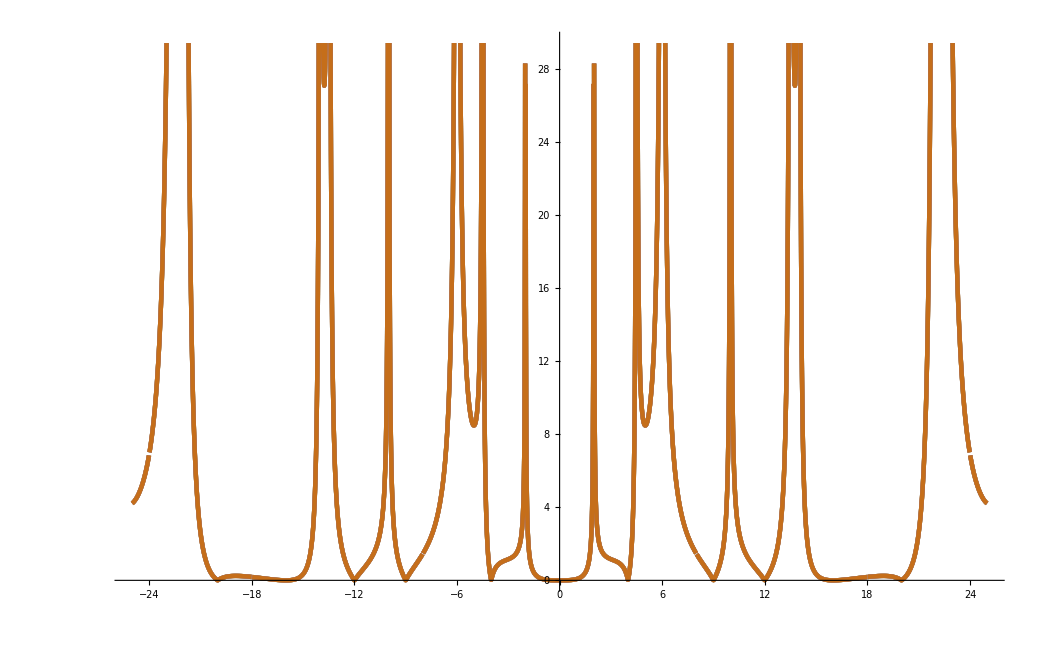

```mathematica
Plot[Table[h[x8,t8,4],{t8,{0,0.01,0.1,0.5,1,20}}]//Evaluate,{x,-25,25}, PlotStyle-> Thickness[0.003], PlotStyle-> "SolarColors"]
```

Exponential Multiplier for Infinite Product of Divisor Waves

```mathematica
J[x9_,t9_,nm9_]:=Product[Sin[(x*Pi)/n],{n,2,nm9}];
```

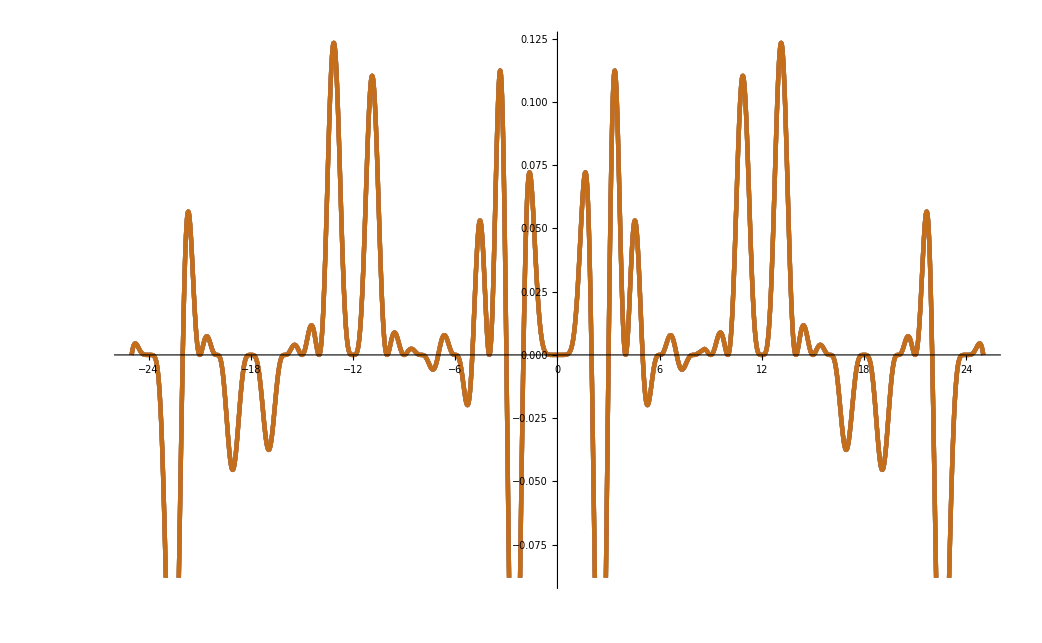

```mathematica
Plot[Table[J[x9,t9,9],{t9,{0,0.01,0.1,0.5,1,20}}]//Evaluate,{x,-25,25}, PlotStyle-> Thickness[0.003], PlotStyle-> "SolarColors"]
```